```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neutron/olcpu/ae_qml/bin

# ROCs w/o btag

## Hybrid Data

```mathematica
baselineTPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/tpr_1.dat","Real32"];
kfold1FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/fpr_1.dat","Real32"];
kfold2FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/fpr_2.dat","Real32"];
kfold3FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/fpr_3.dat","Real32"];
kfold4FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/fpr_4.dat","Real32"];
kfold5FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/fpr_5.dat","Real32"];
hybridFPRs={kfold1FPR, kfold2FPR, kfold3FPR, kfold4FPR, kfold5FPR};
μhybridFPRs = Mean[hybridFPRs];
σhybridFPRs = StandardDeviation[hybridFPRs];hybridAUCs = BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/aucs.dat","Real32"];
μhybridAUC = Mean[hybridAUCs];
σhybridAUC = StandardDeviation[hybridAUCs];
StringForm["AUC: `` ± ``", μhybridAUC, σhybridAUC]
hybridFPRsAtTPR = 1/BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_60to16_nobtag_c0.7/roc_plot/fprs_at_tprs.dat","Real32"];
μhybridFPRsAtTPR = Mean[hybridFPRsAtTPR];
σhybridFPRsAtTPR = StandardDeviation[hybridFPRsAtTPR];
StringForm["FPR @ 80% TPR: `` ± ``", μhybridFPRsAtTPR, σhybridFPRsAtTPR]
```

AUC: 0.720225 ± 0.00524054

FPR @ 80% TPR: 2.04544 ± 0.0494891

## Classical Data

```mathematica
baselineTPR=BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/tpr_1.dat","Real32"];
kfold1FPR=BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_1.dat","Real32"];
kfold2FPR=BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_2.dat","Real32"];
kfold3FPR=BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_3.dat","Real32"];
kfold4FPR=BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_4.dat","Real32"];
kfold5FPR=BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_5.dat","Real32"];
classicalFPRs={kfold1FPR, kfold2FPR, kfold3FPR, kfold4FPR, kfold5FPR};
μclassicalFPRs = Mean[classicalFPRs];
σclassicalFPRs = StandardDeviation[classicalFPRs];
classicalAUCs = BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/aucs.dat","Real32"];
μclassicalAUC = Mean[classicalAUCs];
σclassicalAUC = StandardDeviation[classicalAUCs];
StringForm["AUC: `` ± ``", μclassicalAUC, σclassicalAUC]
classicalFPRsAtTPR = 1/BinaryReadList["trained_nns/60to16_20k_ntest20k_b256_lr0.01/roc_plot/fprs_at_tprs.dat","Real32"];
μclassicalFPRsAtTPR = Mean[classicalFPRsAtTPR];
σclassicalFPRsAtTPR = StandardDeviation[classicalFPRsAtTPR];
StringForm["FPR @ 80% TPR: `` ± ``", μclassicalFPRsAtTPR, σclassicalFPRsAtTPR]
```

AUC: 0.698787 ± 0.00454827

FPR @ 80% TPR: 1.92153 ± 0.0353244

## Two-Step Data

```mathematica
baselineTPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/tpr_1.dat","Real32"];
kfold1FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/fpr_1.dat","Real32"];
kfold2FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/fpr_2.dat","Real32"];
kfold3FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/fpr_3.dat","Real32"];
kfold4FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/fpr_4.dat","Real32"];
kfold5FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/fpr_5.dat","Real32"];
twoStepFPRs={kfold1FPR, kfold2FPR, kfold3FPR, kfold4FPR, kfold5FPR};
μtwoStepFPRs = Mean[twoStepFPRs];
σtwoStepFPRs = StandardDeviation[twoStepFPRs];
twoStepAUCs = BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/aucs.dat","Real32"];
μtwoStepAUC = Mean[twoStepAUCs];
σtwoStepAUC = StandardDeviation[twoStepAUCs];
StringForm["AUC: `` ± ``", μtwoStepAUC, σtwoStepAUC]
twoStepFPRsAtTPR = 1/BinaryReadList["trained_vqcs/vqc_20k_4q_r2_nobtag/roc_plot/fprs_at_tprs.dat","Real32"];
μtwoStepFPRsAtTPR = Mean[twoStepFPRsAtTPR];
σtwoStepFPRsAtTPR = StandardDeviation[twoStepFPRsAtTPR];
StringForm["FPR @ 80% TPR: `` ± ``", μtwoStepFPRsAtTPR, σtwoStepFPRsAtTPR]
```

AUC: 0.507537 ± 0.00271982

FPR @ 80% TPR: 1.26273 ± 0.00369633

## Plots

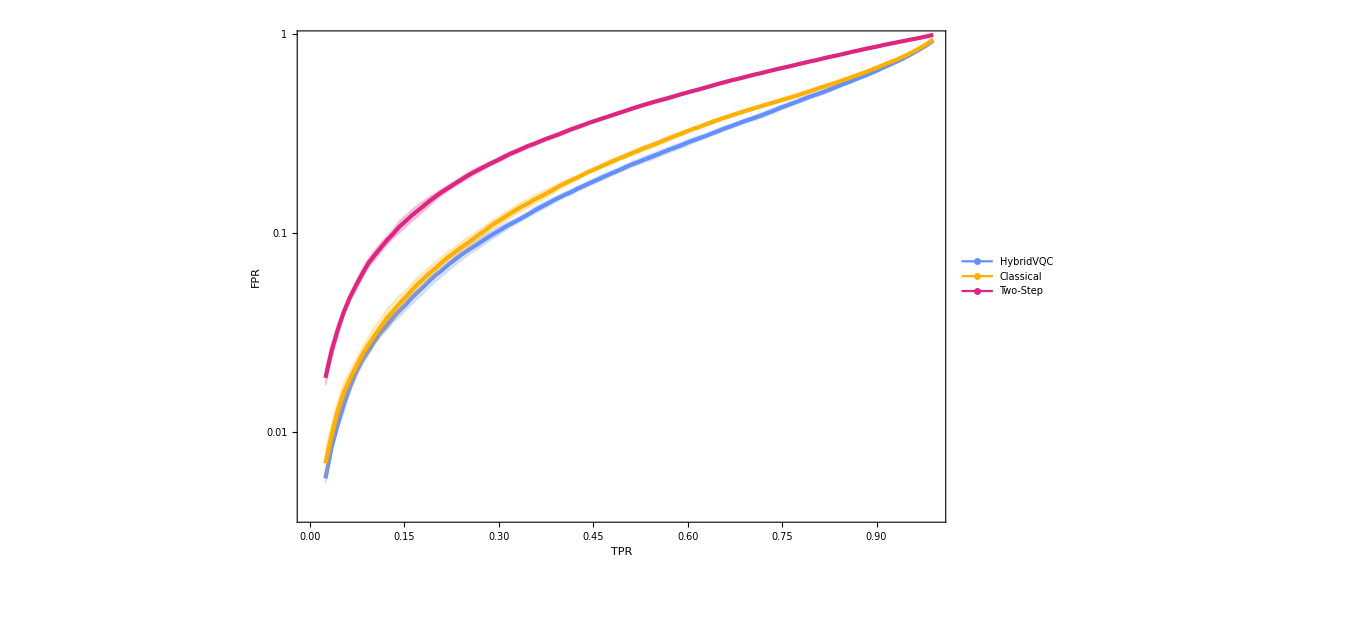

```mathematica
(*Hybrid Model*)
hybridFPRs=μhybridFPRs;
hybridFPRsTop=Table[μhybridFPRs[[i]]+σhybridFPRs[[i]], {i,1,Length@μhybridFPRs}];
hybridFPRsBot=Table[μhybridFPRs[[i]]-σhybridFPRs[[i]], {i,1,Length@μhybridFPRs}];

hybridCurve = Transpose[{baselineTPR, hybridFPRs}];
hybridCurveTop = Transpose[{baselineTPR, hybridFPRsTop}];
hybridCurveBot = Transpose[{baselineTPR, hybridFPRsBot}];

(*Classical Model*)
classicalFPRs=μclassicalFPRs;
classicalFPRsTop=Table[μclassicalFPRs[[i]]+σclassicalFPRs[[i]], {i,1,Length@μclassicalFPRs}];
classicalFPRsBot=Table[μclassicalFPRs[[i]]-σclassicalFPRs[[i]], {i,1,Length@μclassicalFPRs}];

classicalCurve = Transpose[{baselineTPR, classicalFPRs}];
classicalCurveTop = Transpose[{baselineTPR, classicalFPRsTop}];
classicalCurveBot = Transpose[{baselineTPR, classicalFPRsBot}];

(*Two-Step Model*)

(*Plotting*)
hexColors = {"#648FFF","#785EF0","#DC267F","#FE6100","#FFB000"};
hexColors = Map[RGBColor, hexColors];
lighterHexColors = {#, Opacity[0.2]}&/@hexColors;
darkerHexColors = {Darker[#,0.2]}&/@hexColors;

plot=Show[ListLogPlot[hybridCurve, PlotStyle->{hexColors[[1]], Thickness[0.003]},Joined->True],
ListLogPlot[{hybridCurveTop,hybridCurveBot},
PlotStyle->{lighterHexColors[[1]], lighterHexColors[[1]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[1]]],
ListLogPlot[classicalCurve, PlotStyle->{hexColors[[5]], Thickness[0.003]},Joined->True],
ListLogPlot[{classicalCurveTop,classicalCurveBot},
PlotStyle->{lighterHexColors[[5]], lighterHexColors[[5]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[5]]],
ListLogPlot[twoStepCurve, PlotStyle->{hexColors[[3]], Thickness[0.003]},Joined->True],
ListLogPlot[{twoStepCurveTop,twoStepCurveBot},
PlotStyle->{lighterHexColors[[3]], lighterHexColors[[3]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[3]]],
ImageSize->1000, Frame->True, FrameStyle->Directive[20], FrameLabel->{"TPR","FPR"}, ImagePadding->110, ImageResolution->300];

legendPlot = Legended[plot,Placed[LineLegend[{hexColors[[1]], hexColors[[5]], hexColors[[3]]}, {"HybridVQC", "Classical",  "Two-Step"}, LegendMarkers->Graphics[{Thickness[.3], Line[{{0,0},{10,0}}]}],LabelStyle->{18, Bold}],{0.1,0.87}]]
```

```mathematica
Export["paper_plots/ROCs_nobtag.svg",legendPlot]
Export["paper_plots/ROCs_nobtag.pdf",legendPlot]
```

paper_plots/ROCs_nobtag.svg

paper_plots/ROCs_nobtag.pdf

# ROCs w/ btag

## Hybrid Data

```mathematica
baselineTPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/tpr_1.dat","Real32"];
kfold1FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/fpr_1.dat","Real32"];
kfold2FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/fpr_2.dat","Real32"];
kfold3FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/fpr_3.dat","Real32"];
kfold4FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/fpr_4.dat","Real32"];
kfold5FPR=BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/fpr_5.dat","Real32"];
hybridFPRs={kfold1FPR, kfold2FPR, kfold3FPR, kfold4FPR, kfold5FPR};
μhybridFPRs = Mean[hybridFPRs];
σhybridFPRs = StandardDeviation[hybridFPRs];
hybridAUCs = BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/aucs.dat","Real32"];
μhybridAUC = Mean[hybridAUCs];
σhybridAUC = StandardDeviation[hybridAUCs];
StringForm["AUC: `` ± ``", μhybridAUC, σhybridAUC]
hybridFPRsAtTPR = 1/BinaryReadList["trained_vqcs/hybrid_ae_20k_4q_r2_67to16_c0.7/roc_plot/fprs_at_tprs.dat","Real32"];
μhybridFPRsAtTPR = Mean[hybridFPRsAtTPR];
σhybridFPRsAtTPR = StandardDeviation[hybridFPRsAtTPR];
StringForm["FPR @ 80% TPR: `` ± ``", μhybridFPRsAtTPR, σhybridFPRsAtTPR]
```

AUC: 0.732685 ± 0.00358201

FPR @ 80% TPR: 2.13404 ± 0.0281675

## Classical Data

```mathematica
baselineTPR=BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/tpr_1.dat","Real32"];
kfold1FPR=BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_1.dat","Real32"];
kfold2FPR=BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_2.dat","Real32"];
kfold3FPR=BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_3.dat","Real32"];
kfold4FPR=BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_4.dat","Real32"];
kfold5FPR=BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/fpr_5.dat","Real32"];
classicalFPRs={kfold1FPR, kfold2FPR, kfold3FPR, kfold4FPR, kfold5FPR};
μclassicalFPRs = Mean[classicalFPRs];
σclassicalFPRs = StandardDeviation[classicalFPRs];
classicalAUCs = BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/aucs.dat","Real32"];
μclassicalAUC = Mean[classicalAUCs];
σclassicalAUC = StandardDeviation[classicalAUCs];
StringForm["AUC: `` ± ``", μclassicalAUC, σclassicalAUC]
classicalFPRsAtTPR = 1/BinaryReadList["trained_nns/67to16_20k_ntest20k_b256_lr0.01/roc_plot/fprs_at_tprs.dat","Real32"];
μclassicalFPRsAtTPR = Mean[classicalFPRsAtTPR];
σclassicalFPRsAtTPR = StandardDeviation[classicalFPRsAtTPR];
StringForm["FPR @ 80% TPR: `` ± ``", μclassicalFPRsAtTPR, σclassicalFPRsAtTPR]
```

AUC: 0.733979 ± 0.00232286

FPR @ 80% TPR: 2.10754 ± 0.0290871

## Two-Step Data

```mathematica
baselineTPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/tpr_1.dat","Real32"];
kfold1FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/fpr_1.dat","Real32"];
kfold2FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/fpr_2.dat","Real32"];
kfold3FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/fpr_3.dat","Real32"];
kfold4FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/fpr_4.dat","Real32"];
kfold5FPR=BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/fpr_5.dat","Real32"];
twoStepFPRs={kfold1FPR, kfold2FPR, kfold3FPR, kfold4FPR, kfold5FPR};
μtwoStepFPRs = Mean[twoStepFPRs];
σtwoStepFPRs = StandardDeviation[twoStepFPRs];
twoStepAUCs = BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/aucs.dat","Real32"];
μtwoStepAUC = Mean[twoStepAUCs];
σtwoStepAUC = StandardDeviation[twoStepAUCs];
StringForm["AUC: `` ± ``", μtwoStepAUC, σtwoStepAUC]
twoStepFPRsAtTPR = 1/BinaryReadList["trained_vqcs/vqc_20k_4q_r2/roc_plot/fprs_at_tprs.dat","Real32"];
μtwoStepFPRsAtTPR = Mean[twoStepFPRsAtTPR];
σtwoStepFPRsAtTPR = StandardDeviation[twoStepFPRsAtTPR];
StringForm["FPR @ 80% TPR: `` ± ``", μtwoStepFPRsAtTPR, σtwoStepFPRsAtTPR]
```

AUC: 0.560641 ± 0.00288259

FPR @ 80% TPR: 1.36775 ± 0.00672

## Plots

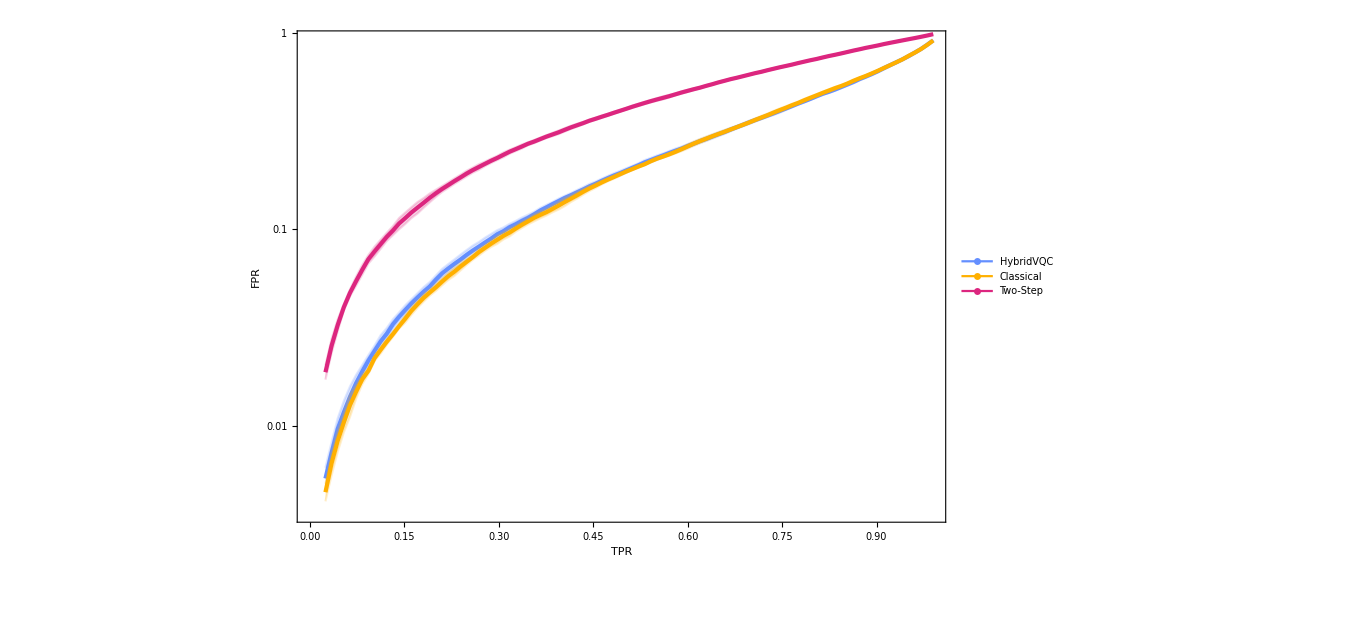

```mathematica
(*Hybrid Model*)
hybridFPRs=μhybridFPRs;
hybridFPRsTop=Table[μhybridFPRs[[i]]+σhybridFPRs[[i]], {i,1,Length@μhybridFPRs}];
hybridFPRsBot=Table[μhybridFPRs[[i]]-σhybridFPRs[[i]], {i,1,Length@μhybridFPRs}];

hybridCurve = Transpose[{baselineTPR, hybridFPRs}];
hybridCurveTop = Transpose[{baselineTPR, hybridFPRsTop}];
hybridCurveBot = Transpose[{baselineTPR, hybridFPRsBot}];

(*Classical Model*)
classicalFPRs=μclassicalFPRs;
classicalFPRsTop=Table[μclassicalFPRs[[i]]+σclassicalFPRs[[i]], {i,1,Length@μclassicalFPRs}];
classicalFPRsBot=Table[μclassicalFPRs[[i]]-σclassicalFPRs[[i]], {i,1,Length@μclassicalFPRs}];

classicalCurve = Transpose[{baselineTPR, classicalFPRs}];
classicalCurveTop = Transpose[{baselineTPR, classicalFPRsTop}];
classicalCurveBot = Transpose[{baselineTPR, classicalFPRsBot}];

(*Two-Step Model*)
twoStepFPRs=μtwoStepFPRs;
twoStepFPRsTop=Table[μtwoStepFPRs[[i]]+σtwoStepFPRs[[i]], {i,1,Length@μtwoStepFPRs}];
twoStepFPRsBot=Table[μtwoStepFPRs[[i]]-σtwoStepFPRs[[i]], {i,1,Length@μtwoStepFPRs}];

twoStepCurve = Transpose[{baselineTPR, twoStepFPRs}];
twoStepCurveTop = Transpose[{baselineTPR, twoStepFPRsTop}];
twoStepCurveBot = Transpose[{baselineTPR, twoStepFPRsBot}];

(*Plotting*)
hexColors = {"#648FFF","#785EF0","#DC267F","#FE6100","#FFB000"};
hexColors = Map[RGBColor, hexColors];
lighterHexColors = {#, Opacity[0.2]}&/@hexColors;
darkerHexColors = {Darker[#,0.2]}&/@hexColors;

plot=Show[ListLogPlot[hybridCurve, PlotStyle->{hexColors[[1]], Thickness[0.003]},Joined->True],
ListLogPlot[{hybridCurveTop,hybridCurveBot},
PlotStyle->{lighterHexColors[[1]], lighterHexColors[[1]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[1]]],
ListLogPlot[classicalCurve, PlotStyle->{hexColors[[5]], Thickness[0.003]},Joined->True],
ListLogPlot[{classicalCurveTop,classicalCurveBot},
PlotStyle->{lighterHexColors[[5]], lighterHexColors[[5]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[5]]],
ListLogPlot[twoStepCurve, PlotStyle->{hexColors[[3]], Thickness[0.003]},Joined->True],
ListLogPlot[{twoStepCurveTop,twoStepCurveBot},
PlotStyle->{lighterHexColors[[3]], lighterHexColors[[3]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[3]]],
ImageSize->1000, Frame->True, FrameStyle->Directive[20], FrameLabel->{"TPR","FPR"}, ImagePadding->110, ImageResolution->300];

legendPlot = Legended[plot,Placed[LineLegend[{hexColors[[1]], hexColors[[5]], hexColors[[3]]}, {"HybridVQC", "Classical",  "Two-Step"}, LegendMarkers->Graphics[{Thickness[.3], Line[{{0,0},{10,0}}]}],LabelStyle->{18, Bold}],{0.1,0.87}]]
```

```mathematica
Export["paper_plots/ROCs.svg",legendPlot]
Export["paper_plots/ROCs.pdf",legendPlot]
```

paper_plots/ROCs.svg

paper_plots/ROCs.pdf